```mathematica
SeedRandom[20230405];
data1=RandomReal[BinormalDistribution[{-2,3},{5,1},0.5],500];
```

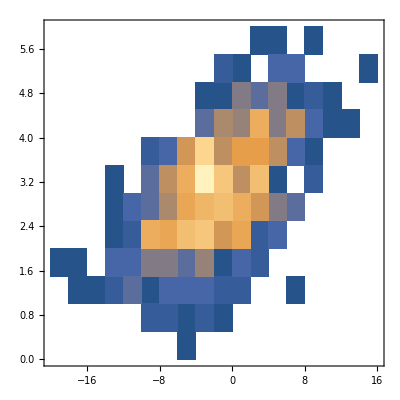

```mathematica
DensityHistogram[data1]
```

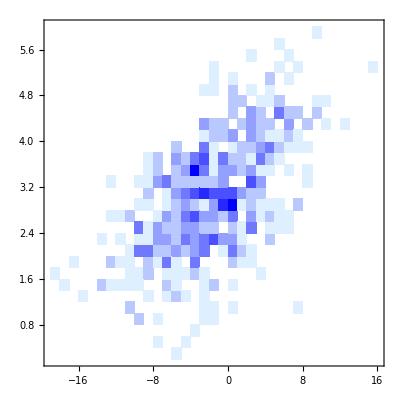

```mathematica
DensityHistogram[data1,30,ColorFunction->(Blend[{LightBlue,Blue},#]&)]
```

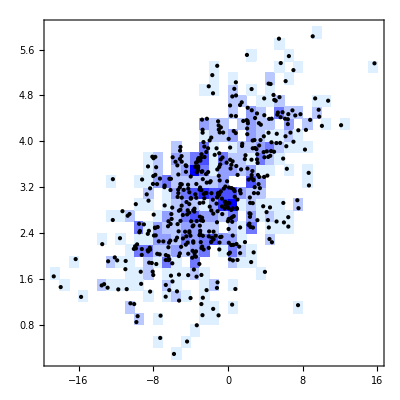

```mathematica
DensityHistogram[data1,30,ColorFunction->(Blend[{LightBlue,Blue},#]&),ChartElementFunction->({ChartElementData["Rectangle"][##],Opacity[1,Black],AbsolutePointSize@3,Point@#2}&)]
```

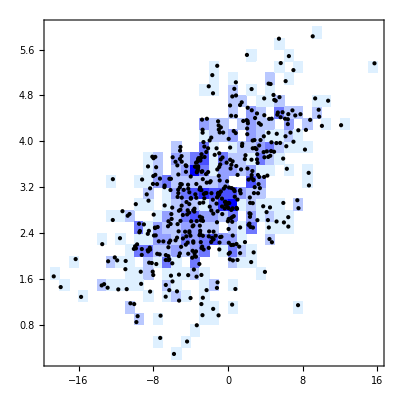

```mathematica
DensityHistogram[data1,30,ColorFunction->(Blend[{LightBlue,Blue},#]&),Epilog->{First[ListPlot[data1,PlotStyle->Directive[Black,AbsolutePointSize@3]]]}]
```

```mathematica
Multicolumn[DensityHistogram[data1,30,ColorFunction->(Blend[{LightBlue,Blue},#]&),Epilog->{First[ListPlot[data1,PlotStyle->Directive[Black,AbsolutePointSize@3]]]},Method->{"DistributionAxes"->#},PlotLabel->Style[#,16],ImageSize->Medium]&/@{"Histogram","Lines","BoxWhisker","SmoothHistogram"},2]
```

-Graphics-
-Graphics-

```mathematica
Multicolumn[DensityHistogram[data1,30,ColorFunction->(White&),Epilog->{First[ListPlot[data1,PlotStyle->Directive[Black,AbsolutePointSize@3]]]},Method->{"DistributionAxes"->#},PlotLabel->Style[#,16],ImageSize->Medium,Frame->{True,True,False,False}]&/@{"Histogram","Lines","BoxWhisker","SmoothHistogram"},2]
```

-Graphics-
-Graphics-

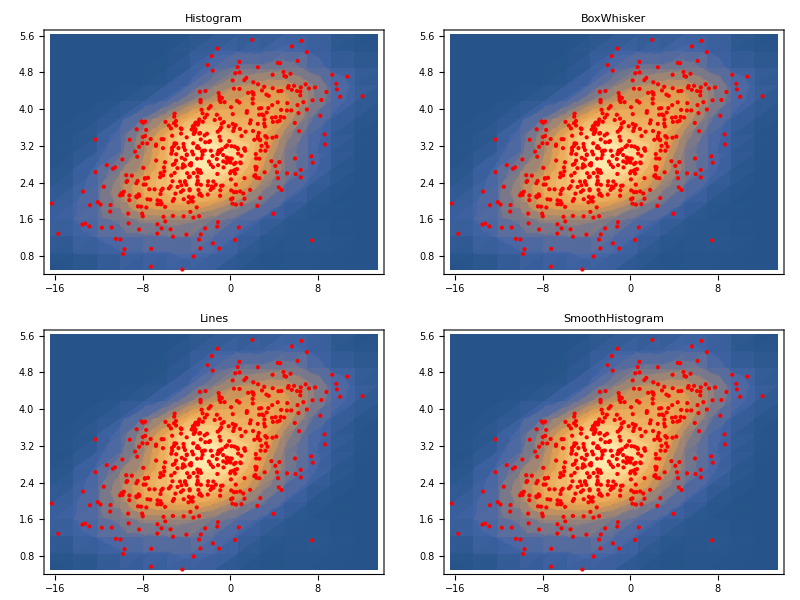

```mathematica
Multicolumn[SmoothDensityHistogram[data1,Epilog->{First[ListPlot[data1,PlotStyle->Directive[Red,AbsolutePointSize@3]]]},Mesh->10,MeshStyle->Directive[Black,Thick,Dashed],Method->{"DistributionAxes"->#},PlotLabel->Style[#,16],ImageSize->Medium]&/@{"Histogram","Lines","BoxWhisker","SmoothHistogram"},2]
```

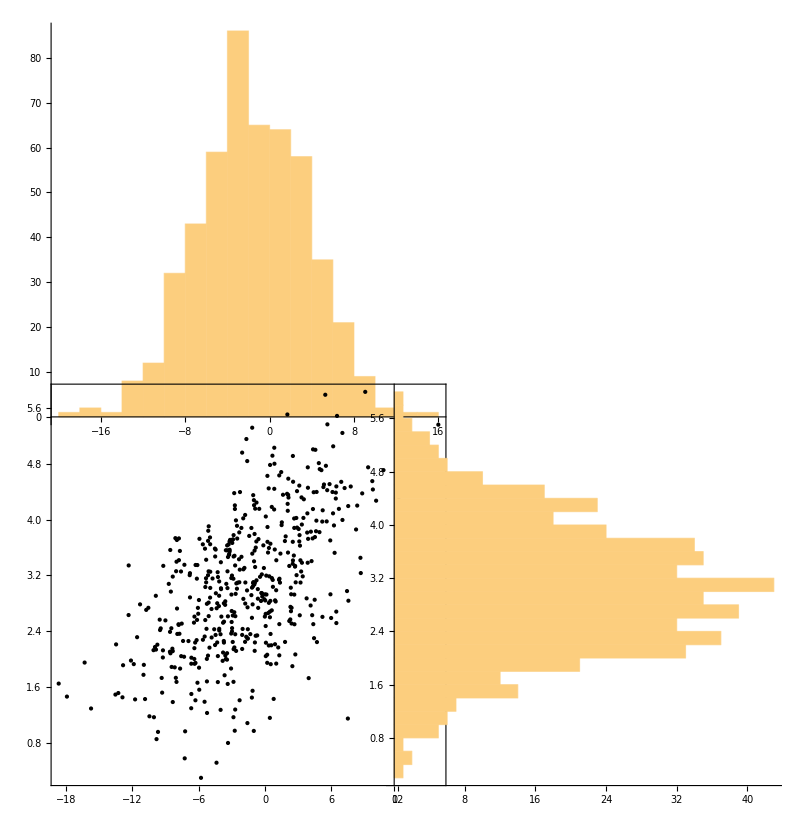

```mathematica
SeedRandom[20230405];
data1=RandomReal[BinormalDistribution[{-2,3},{5,1},0.5],500];
{histData1,histData2}=Transpose@data1;
histPlot1=Histogram[histData1,15,AspectRatio->1/2,PerformanceGoal->"Quality"];
histPlot2=Histogram[histData2,30,AspectRatio->3,BarOrigin->Left];
data1Plot=Graphics[Point@data1,Frame->True,AspectRatio->1];
boxPlot1=BoxWhiskerChart[histData1,Frame->False,BarOrigin->Left,AspectRatio->1];
boxPlot2=BoxWhiskerChart[histData2,Frame->False,AspectRatio->1];
GraphicsGrid[{{histPlot1},{data1Plot,histPlot2}},Spacings->{-100,-80},ImagePadding->{{130,60},{120,60}}]
```

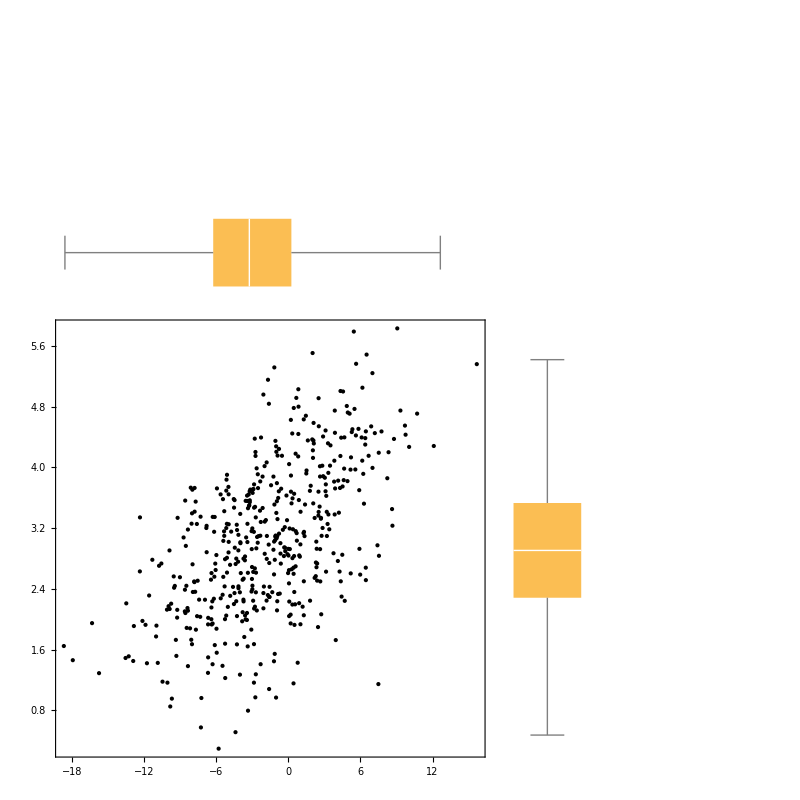

```mathematica
GraphicsGrid[{{boxPlot1},{data1Plot,boxPlot2}},Spacings->{-150,-150},ImagePadding->{{160,40},{140,25}}]
```

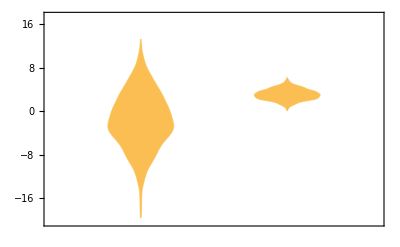

```mathematica
DistributionChart[{histData1,histData2}]
```

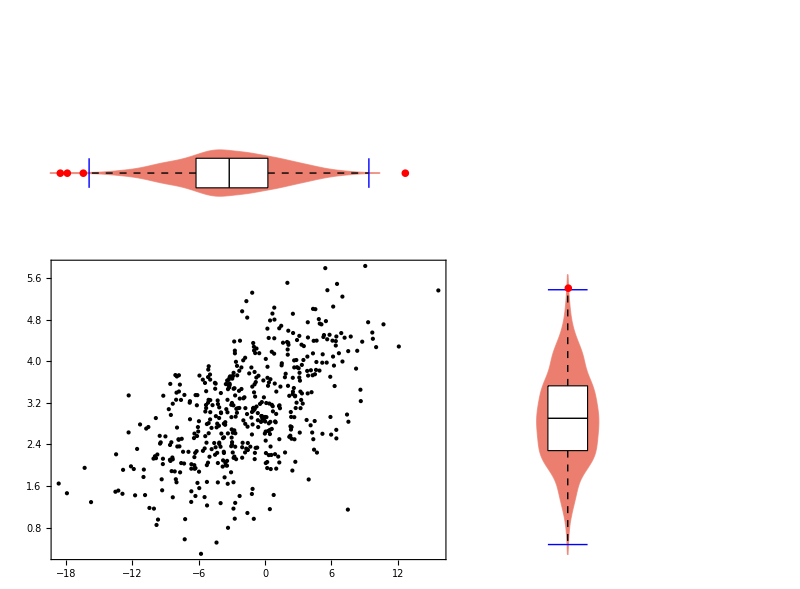

```mathematica
DCPlot1=Show[DistributionChart[histData1,ChartStyle->24,Frame->False,BarOrigin->Left],BoxWhiskerChart[histData1,{{"MedianMarker",1,Directive[Black,Thickness->0.008]},{"Outliers","●",Red},{"Whiskers",Directive[Dashed]},{"Fences",1,Directive[Blue,Thickness->0.003]}},BarSpacing->3,ChartStyle->Directive[EdgeForm[Black],White],Frame->False,BarOrigin->Left]];
DCPlot2=Show[DistributionChart[histData2,ChartStyle->24,Frame->False],BoxWhiskerChart[histData2,{{"MedianMarker",1,Directive[Black,Thickness->0.008]},{"Outliers","●",Red},{"Whiskers",Directive[Dashed]},{"Fences",1,Directive[Blue,Thickness->0.003]}},BarSpacing->3,ChartStyle->Directive[EdgeForm[Black],White],Frame->False]];
GraphicsGrid[{{DCPlot1},{data1Plot,DCPlot2}},Spacings->{-100,-80},ImagePadding->{{130,50},{120,60}}]
```

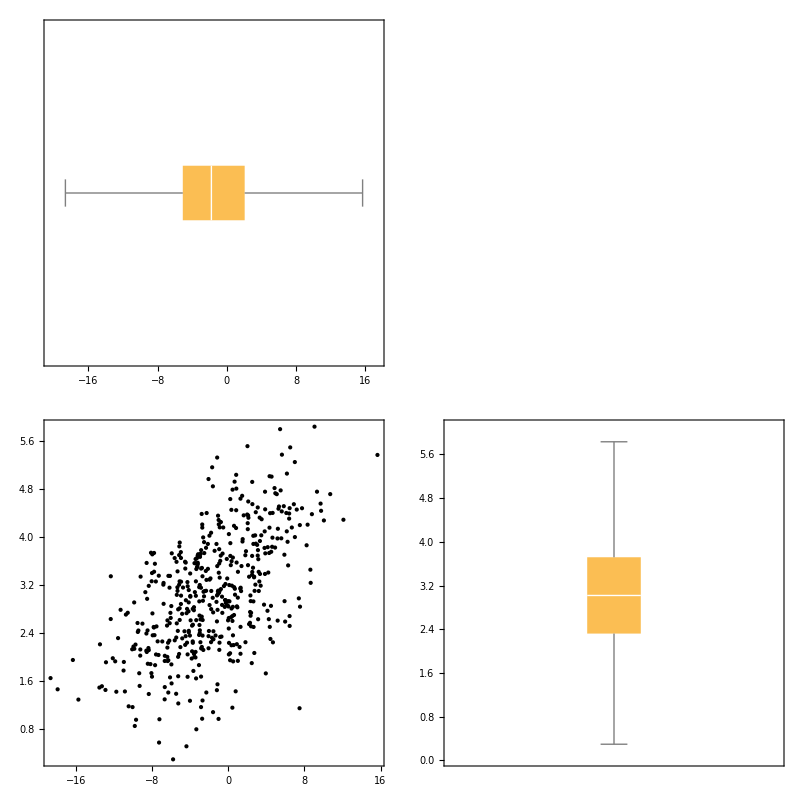

```mathematica
SeedRandom[20230405];
data1=RandomReal[BinormalDistribution[{-2,3},{5,1},0.5],500];
{histData1,histData2}=Transpose@data1;
data1Plot=Graphics[Point@data1,Frame->True,AspectRatio->1];
boxPlot1=BoxWhiskerChart[histData1,Frame->{True,False,False,False},BarOrigin->Left,AspectRatio->1];
boxPlot2=BoxWhiskerChart[histData2,Frame->{False,True,False,False},AspectRatio->1];
GraphicsGrid[{{boxPlot1},{data1Plot,boxPlot2}},Spacings->{0,0},ImagePadding->{{160,40},{140,20}}]
```